# Chapter. Rotating disk electrode voltammetry

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
Off[Solve::"svars"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->247,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12],Cell[TextData[{"Rotating disk electrode voltammetry"}],FontFamily->"Arial",FontSize->12],None},{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Determining the velocity profile","Analytical solution","Finite differences solution","Further reading"},#]&)]],FontFamily->"Arial",FontSize->12],Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"GraphicsPrintingFormat"->"DownloadPostScript",
"FirstPageFace"->Left,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];
SetSystemOptions["TypesetOptions"->{"IconicElidedForms"->False}]
```

TypesetOptions→{ColorDirectiveSwatches→True,EmbedButtonByteCountLimit→134217728,IconicElidedForms→False,InterpretableElidedForms→False,NumericalApproximationForms→True,ParenthesizeScriptBase→False,TransformationFunctionElidedThreshold→4}

```mathematica
ClearNotations[];
Symbolize[Subscript[c, _]];
Symbolize[c^_];
```

```mathematica
$TextStyle= {FontFamily-> "Arial",FontSize-> 10, FontWeight->Plain};
$FrameStyle={Black,AbsoluteThickness[.5]};
$ImageSize=288;
```

```mathematica
SetOptions[Plot,
Axes->False,
Frame->True,
FrameStyle->$FrameStyle,
GridLines->None,
ImageSize-> $ImageSize,
PlotStyle->{Red,AbsoluteThickness[.5]}];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
Frame->True,
FrameStyle->$FrameStyle,
GridLines->None,
ImageSize->$ImageSize,
PlotStyle->{Red,AbsoluteThickness[.5]},
Joined->True];
```

```mathematica
ClearAll[popUpAnimation];

SetAttributes[popUpAnimation, HoldFirst]

popUpAnimation[expr_, windowSize_List:{288,288}] :=CreateDocument[Cell[ ToBoxes@ListAnimate[expr]],
"BlinkingCellInsertionPoint"->False,
"CellInsertionPointCell"->None,
"GhostCellInEmptyNotebook"->True,
"TrackCellChangeTimes"->False,
Background->White,
CellFrame->False,
CellFrameLabelMargins->0,
CellLabelMargins->0,
CellMargins->0,
CellContext->Notebook,
WindowSize ->  windowSize,
WindowFrame ->  "Palette",
WindowElements ->{"StatusArea"},
WindowTitle ->"Animation",
Magnification-> 1,
ShowCellBracket -> False]
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

Rotating disk electrode voltammetry is a very commonly used experimental method. The end of a cylinder, comprised of an electrode embedded in an inert material is placed in solution and rotated about the axis r=0 as shown in Fig. Chapter.FigureCaption. The rotation sweeps fluid near the disk surface outwards in the radial direction. This fluid is replace by fluid flowing to the disk in the z direction.

code for Fig. Chapter.FigureCaption

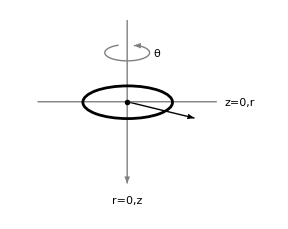

```mathematica
label1=DisplayForm[RowBox[{TraditionalForm[MakeBoxes[r=0,TraditionalForm]],Style[",",FontFamily-> "TimesNewRoman"],TraditionalForm[z]}]];

label2=DisplayForm[RowBox[{TraditionalForm[MakeBoxes[z=0,TraditionalForm]],Style[",",FontFamily-> "TimesNewRoman"],TraditionalForm[r]}]];

label3=DisplayForm[RowBox[{TraditionalForm[θ]}]];

Graphics[{
Arrowheads[Small],
Arrow[{{.5,.5},{.8,.4}}],
Text[label3,{.63,.8}],Text[label2,{1.0,.5}],Text[label1,{.5,-.1}],GrayLevel[.5],Arrow[{{.5,1},{.5,0}}],
Arrow[{{.535,.843},{.53,.843}}],
Circle[{.5,.8},{.1,.05},{(5 π)/8,(9.5 π)/4}],
Line[{{.1,.5},{.9,.5}}],GrayLevel[0],AbsoluteThickness[2],AbsolutePointSize[4],Point[{.5,.5}],Circle[{.5,.5},{.2,.1}]},
AspectRatio->.8,
ImagePadding->0,
ImageSize->288,
PlotRange->{{0.05,1.1},{-.15,1}},
PlotRangePadding->0]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
$Line=0;
```

Fig. Chapter.FigureCaption  Coordinates of the rotating disk system. r is the radial distance from the axis of rotation, z is the distance perpendicular to the electrode surface.

The coordinate system can be animated and sent to a separate pop up window. To modify the size of the pop-up window change the parameters that are currently set at {260, 260}.

```mathematica
Clear[dots];

dots=Table[{.5+2*.2*Cos[θ],.5+.2*Sin[θ]},{θ,-π/4,7*π/4,π/16}];

(*double click on the figure to restart the animation*)
popUpAnimation[rde=Table[
Graphics[{Text[θ,{.63,.8}],Text[label2,{.05,.5}],Text[label1,{.5,-.1}],GrayLevel[.5],
Arrow[{{.5,1},{.5,0}}],
Arrow[{{.535,.843},{.53,.843}}],
Circle[{.5,.8},{.1,.05},{5*π/8,9.5*π/4}],Line[{{0.1,.5},{.9,.5}}],GrayLevel[0],Arrow[{{.5,.5},dots⟦j⟧}],AbsoluteThickness[2],AbsolutePointSize[4],Point[{.5,.5}],Circle[{.5,.5},{.2,.1}]},ImageSize->288],{j,1,Length[dots]}],{330,436}(*<-- window size*)];
```

```mathematica
(*Export the animation*)
Export["rde.gif",rde,"GIF","DisposalOperation"-> Background,"AnimationRepetitions"-> 10,"AnimationDisplayTime"-> .1];
```

All the previous electrochemical methods discussed in this book it was assumed that diffusion was the only mode of transporting molecules to the electrode surface. In rotating disk voltammetry convection needs to be included in the mass transport equations and thus the velocity of the liquid needs to be determined. The chapter begins by showing how to determine the velocity of the liquid and then shows how rotating disk voltammetry can be simulated in both steady state and non-steady state conditions.

Chapter.Section Determining the velocity profile

To determine the velocity of fluid to a rotating disk two equations, one for conservation of mass and the other for conservation of momentum, must be solved. In the solution below the fluid is assumed to have constant density and viscosity. The conservation of mass equation is known as the continuity equation:

∇·v=0

In eqn (Chapter.EquationNumbered) v is the velocity vector:

v=v_r i_r+v_θ i_θ+v_z i_z

where i is a unit vector and v_r, v_θ, and v_z are the scalar velocities in the r, θ and z directions respectively. The conservation of momentum equation is known as the Navier-Stokes equation:

dv/dt+v·∇v=-1/ρ∇𝒫+ν∇^2 v

where ν is the kinematic viscosity, which is defined as viscosity divided by density, ρ is the density, and 𝒫 is the dynamic pressure:

∇𝒫=∇p-ρ g

where p is the pressure and g is gravitational acceleration.
To determine the velocity of liquid to the rotating disk electrode it is appropriate to work in cylindrical coordinates. The components of the liquid velocity in the r, θ, and z directions can be gathered in a list:

```mathematica
ClearAll[v,vr,vz,vθ];
(*velocity*)
v={vr[r,θ,z,t],vθ[r,θ,z,t],vz[r,θ,z,t]};
```

Equation (Chapter.EquationNumbered) is then transformed to cylindrical coordinates.

```mathematica
eqn1=Expand[Div[v,{r,θ,z},"Cylindrical"]]== 0
```

vr[r,θ,z,t]/r+vz^(0,0,1,0)[r,θ,z,t]+(vθ^(0,1,0,0)[r,θ,z,t])/r+vr^(1,0,0,0)[r,θ,z,t]==0

Equation (Chapter.EquationNumbered) becomes:

v_r/r+(∂v_r)/(∂r)+1/r(∂v_θ)/(∂θ)+(∂v_z)/(∂r)=0

Equation (Chapter.EquationNumbered) can be split into four parts each of which are transformed to cylindrical coordinates.

```mathematica
part1=D[v,t]
```

{vr^(0,0,0,1)[r,θ,z,t],vθ^(0,0,0,1)[r,θ,z,t],vz^(0,0,0,1)[r,θ,z,t]}

Making use of the identity

v·∇v=1/2∇(v·v)-v×curl  v

where × is the vector or cross product, gives:

```mathematica
part2=Grad[v.v,{r,θ,z},"Cylindrical"]/2-Cross[v,Curl[v,{r,θ,z},"Cylindrical"]]//Expand
```

{-vθ[r,θ,z,t]^2/r+vz[r,θ,z,t] vr^(0,0,1,0)[r,θ,z,t]+(vθ[r,θ,z,t] vr^(0,1,0,0)[r,θ,z,t])/r+vr[r,θ,z,t] vr^(1,0,0,0)[r,θ,z,t],(vr[r,θ,z,t] vθ[r,θ,z,t])/r+vz[r,θ,z,t] vθ^(0,0,1,0)[r,θ,z,t]+(vθ[r,θ,z,t] vθ^(0,1,0,0)[r,θ,z,t])/r+vr[r,θ,z,t] vθ^(1,0,0,0)[r,θ,z,t],vz[r,θ,z,t] vz^(0,0,1,0)[r,θ,z,t]+(vθ[r,θ,z,t] vz^(0,1,0,0)[r,θ,z,t])/r+vr[r,θ,z,t] vz^(1,0,0,0)[r,θ,z,t]}

```mathematica
part3=-Grad[𝒫[r,θ,z,t],{r,θ,z},"Cylindrical"]/ρ//Simplify
```

{-(𝒫^(1,0,0,0)[r,θ,z,t])/ρ,-(𝒫^(0,1,0,0)[r,θ,z,t])/(r ρ),-(𝒫^(0,0,1,0)[r,θ,z,t])/ρ}

```mathematica
part4=ν*Laplacian[v,{r,θ,z},"Cylindrical"]//Simplify
```

{1/r^2 ν (-vr[r,θ,z,t]+r^2 vr^(0,0,2,0)[r,θ,z,t]-2 vθ^(0,1,0,0)[r,θ,z,t]+vr^(0,2,0,0)[r,θ,z,t]+r vr^(1,0,0,0)[r,θ,z,t]+r^2 vr^(2,0,0,0)[r,θ,z,t]),1/r^2 ν (-vθ[r,θ,z,t]+r^2 vθ^(0,0,2,0)[r,θ,z,t]+2 vr^(0,1,0,0)[r,θ,z,t]+vθ^(0,2,0,0)[r,θ,z,t]+r vθ^(1,0,0,0)[r,θ,z,t]+r^2 vθ^(2,0,0,0)[r,θ,z,t]),ν (vz^(0,0,2,0)[r,θ,z,t]+(vz^(0,2,0,0)[r,θ,z,t])/r^2+(vz^(1,0,0,0)[r,θ,z,t])/r+vz^(2,0,0,0)[r,θ,z,t])}

The four parts of the equation, each being a list of three elements, can then be re-joined to produce the r, θ, and z components of eqn (Chapter.EquationNumbered).

```mathematica
eqns=(Expand[part1⟦#⟧+part2⟦#⟧]== Expand[part3⟦#⟧+part4⟦#⟧])&/@{1,2,3};//Simplify
```

Axial symmetry and steady flow require that derivatives with respect to t and θ are zero. A rule replacement list is used to set these derivatives to zero.

```mathematica
eqns=eqns/.{
Derivative[0,0,0,_][x_][y___]-> 0*x,
Derivative[0,_,0,0][x_][y___]-> 0*x}/.{Derivative[a_,b_,c_,_][x_][d_,e_,f_,g_]-> Derivative[a,b,c][x][d,e,f],vθ[d_,e_,f_,g_]->vθ[d,e,f],
vr[d_,e_,f_,g_]->vr[d,e,f],
vz[d_,e_,f_,g_]->vz[d,e,f]};

eqn1=eqn1/.{
Derivative[0,0,0,_][x_][y___]-> 0*x,
Derivative[0,_,0,0][x_][y___]-> 0*x}/.{Derivative[a_,b_,c_,_][x_][d_,e_,f_,g_]-> Derivative[a,b,c][x][d,e,f],vθ[d_,e_,f_,g_]->vθ[d,e,f],
vr[d_,e_,f_,g_]->vr[d,e,f],
vz[d_,e_,f_,g_]->vz[d,e,f]};
```

The three components of eqn (Chapter.EquationNumbered) are:

```mathematica
eqn2=eqns⟦1⟧
```

-vθ[r,θ,z]^2/r+vz[r,θ,z] vr^(0,0,1)[r,θ,z]+vr[r,θ,z] vr^(1,0,0)[r,θ,z]==-(ν vr[r,θ,z])/r^2+ν vr^(0,0,2)[r,θ,z]+(ν vr^(1,0,0)[r,θ,z])/r-(𝒫^(1,0,0)[r,θ,z])/ρ+ν vr^(2,0,0)[r,θ,z]

the r component:

v_r(∂v_r)/(∂r)+v_z(∂v_r)/(∂z)-v_θ^2/r=-1/ρ(∂p)/(∂r)+ν((∂^2 v_r)/(∂r^2)-v_r/r^2+1/r(∂v_r)/(∂r)+(∂^2 v_r)/(∂z^2))

```mathematica
eqn3=eqns⟦2⟧
```

(vr[r,θ,z] vθ[r,θ,z])/r+vz[r,θ,z] vθ^(0,0,1)[r,θ,z]+vr[r,θ,z] vθ^(1,0,0)[r,θ,z]==-(ν vθ[r,θ,z])/r^2+ν vθ^(0,0,2)[r,θ,z]+(ν vθ^(1,0,0)[r,θ,z])/r+ν vθ^(2,0,0)[r,θ,z]

the θ component,

v_r(∂v_θ)/(∂r)+v_z(∂v_θ)/(∂z)+(v_θ v_r)/r=ν((∂^2 v_θ)/(∂r^2)+1/r(∂v_θ)/(∂r)+(∂^2 v_θ)/(∂z^2)-v_θ/r^2)

```mathematica
eqn4=eqns⟦3⟧
```

vz[r,θ,z] vz^(0,0,1)[r,θ,z]+vr[r,θ,z] vz^(1,0,0)[r,θ,z]==-(𝒫^(0,0,1)[r,θ,z])/ρ+ν vz^(0,0,2)[r,θ,z]+(ν vz^(1,0,0)[r,θ,z])/r+ν vz^(2,0,0)[r,θ,z]

and the z component

v_r(∂v_z)/(∂r)+v_z(∂v_z)/(∂z)=-1/ρ(∂p)/(∂z)+ν((∂^2 v_z)/(∂r^2)+1/r(∂v_z)/(∂r)+(∂^2 v_z)/(∂z^2))

The boundary conditions at the disk surface are:

v_r=0
 v_θ=ω
v_z=0

where ω is the rotational speed of the disk. Far away from the surface the boundary conditions are:

v_r=0
v_θ=0
v_z= constant

von Kármán used a separation of variables method to derive a solution using the following replacements:

v_r=r f(z)
 v_θ=r g(z)
v_z=h(z)
p=p(z)

These replacements can be made to eqn1, eqn2, eqn3, and eqn4. It is convenient to put all the replacement rules into one list.

```mathematica
rules={
vr[r,θ,z]-> r*f[z],vθ[r,θ,z]-> r*g[z],
vz[r,θ,z]-> h[z],𝒫[r,θ,z]-> p[z],D[vr[r,θ,z],r]-> D[r*f[z],r],D[vr[r,θ,z],{r,2}]-> D[r*f[z],{r,2}],D[vr[r,θ,z],z]-> D[r*f[z],z],D[vr[r,θ,z],{z,2}]-> D[r*f[z],{z,2}],D[vz[r,θ,z],z]-> h'[z],
D[vz[r,θ,z],r]->0,D[vz[r,θ,z],{z,2}]-> D[h[z],{z,2}],D[𝒫[r,θ,z],r]-> 0,D[𝒫[r,θ,z],z]-> D[p[z],z],
D[vz[r,θ,z],{r,2}]->0,D[vθ[r,θ,z],r]->D[ r*g[z],r],
D[vθ[r,θ,z],{r,2}]->D[ r*g[z],{r,2}],D[vθ[r,θ,z],z]->D[ r*g[z],z],
D[vθ[r,θ,z],{z,2}]->D[ r*g[z],{z,2}]
};
```

```mathematica
eqn1=eqn1/.rules
```

2 f[z]+h'[z]==0

```mathematica
eqn2=eqn2/.rules
```

r f[z]^2-r g[z]^2+r h[z] f'[z]==r ν f''[z]

```mathematica
eqn3=eqn3/.rules
```

2 r f[z] g[z]+r h[z] g'[z]==r ν g''[z]

```mathematica
eqn4=eqn4/.rules
```

h[z] h'[z]==-p'[z]/ρ+ν h''[z]

Equations (Chapter.EquationNumbered) to (Chapter.EquationNumbered) therefore become:

2f(z)+h'(z)=0
(f(z))^2-(g(z))^2+h(z)f'(z)=ν f''(z)
2f(z)g(z)+h(z)g'(z)=ν g''(z)
ρ h(z)h'(z)+p'(z)=νρ h''(z)

The transformed boundary conditions are:

f(0)=h(0)=0 
g(0)=ω/r
 f(∞)= g(∞)=0 
h(∞)=constant

Next step is to make the equations dimensionless by making the following transformations:

γ=(z(ω/ν))^(1/2)
f(z)= ωF(γ)
 g(z)= ω G(γ)
h(z)=-(ων)^(1/2)H(γ)
p(z)=νρωP

Note that the fluid velocity in the z direction (normal to the electrode surface) is independent of both r and θ. Another list of rule replacements is made to transform the equations to dimensionless form.

```mathematica
Clear[rules2,F,G,H];

dγdz=D[z*(ω/ν)^(1/2),z];

rules2={
f[z]-> ω*F[γ],f'[z]-> dγdz*ω*F'[γ],
f''[z]-> dγdz^2*ω*F''[γ],h[z]->- √(ω*ν)*H[γ],
h'[z]->- dγdz*√(ω*ν)*H'[γ],
h''[z]-> -dγdz^2*ω^(1/2)*ν^(1/2)*H''[γ],
g[z]-> ω*G[γ],g'[z]-> dγdz*ω*G'[γ],
g''[z]-> dγdz^2*ω*G''[γ],p'[z]-> dγdz*ρ*ν*ω*P'[γ]
};
```

```mathematica
eqn1=FullSimplify[eqn1/.rules2,{ω>0,ν>0}]
```

2 F[γ]==H'[γ]

```mathematica
eqn2=FullSimplify[eqn2/.rules2,{ω>0,ν>0,r>0}]
```

F[γ]^2==G[γ]^2+H[γ] F'[γ]+F''[γ]

```mathematica
eqn3=FullSimplify[eqn3/. rules2,{ω>0,ν>0,r>0}]
```

2 F[γ] G[γ]==H[γ] G'[γ]+G''[γ]

```mathematica
eqn4=FullSimplify[eqn4/.rules2,{ω>0,ν>0}]
```

H[γ] H'[γ]+P'[γ]+H''[γ]==0

The dimensionless equations to be solved are therefore:

2F(γ)+H'(γ)=0
(F(γ))^2+H(γ)F'(γ)=(G(γ))^2+F''(γ)
2F(γ)G(γ)+H(γ)G'(γ)=G''(γ)
H(γ)H'(γ)+P'(γ)=H''(γ)

with the boundary conditions:

F(0)=H(0)=P(0)=0
G(0)=1
F(∞)=G(∞)=0

Equations (Chapter.EquationNumbered) are non-linear but a solution can be obtained numerically via a series expansion. A Mathematica solution to this problem has been developed by Brian Higgins, formerly of University of California, Davis. The three functions F, G and H can be expanded using Series.

```mathematica
expansion=Series[{F[γ],G[γ],H[γ]},{γ,0,5}]
```

{F[0]+F'[0] γ+1/2 F''[0] γ^2+1/6 F^(3)[0] γ^3+1/24 F^(4)[0] γ^4+1/120 F^(5)[0] γ^5+O[γ]^6,G[0]+G'[0] γ+1/2 G''[0] γ^2+1/6 G^(3)[0] γ^3+1/24 G^(4)[0] γ^4+1/120 G^(5)[0] γ^5+O[γ]^6,H[0]+H'[0] γ+1/2 H''[0] γ^2+1/6 H^(3)[0] γ^3+1/24 H^(4)[0] γ^4+1/120 H^(5)[0] γ^5+O[γ]^6}

Next step is to use Thread to create a list of replacement rules from the series expansions for later substitution.

```mathematica
Thread[{F[γ],G[γ],H[γ]}-> expansion]
```

{F[γ]→F[0]+F'[0] γ+1/2 F''[0] γ^2+1/6 F^(3)[0] γ^3+1/24 F^(4)[0] γ^4+1/120 F^(5)[0] γ^5+O[γ]^6,G[γ]→G[0]+G'[0] γ+1/2 G''[0] γ^2+1/6 G^(3)[0] γ^3+1/24 G^(4)[0] γ^4+1/120 G^(5)[0] γ^5+O[γ]^6,H[γ]→H[0]+H'[0] γ+1/2 H''[0] γ^2+1/6 H^(3)[0] γ^3+1/24 H^(4)[0] γ^4+1/120 H^(5)[0] γ^5+O[γ]^6}

The series expansions for F, G and H are substituted into the first three equations from (Chapter.EquationNumbered) which are represented as variables eqn1, eqn2, and eqn3.

```mathematica
ClearAll[F,G,H,γ]

(*shortened output*)
Short[expansion2={eqn1,eqn2,eqn3}/.Thread[{F[γ],G[γ],H[γ]}-> expansion],4]
```

{2 F[0]+2 F'[0] γ+F''[0] γ^2+1/3 F^(3)[0] γ^3+1/12 F^(4)[0] γ^4+1/60 F^(5)[0] γ^5+O[γ]^6==H'[γ],«1»,2 F[0] G[0]+2 (G[0] F'[0]+F[0] G'[0]) γ+2 («1») γ^2+«1»+2 («1») γ^4+2 (1/12 G''[0] F^(3)[0]+1/12 F''[0] G^(3)[0]+1/24 G'[0] F^(4)[0]+1/24 F'[0] G^(4)[0]+1/120 G[0] F^(5)[0]+1/120 F[0] G^(5)[0]) γ^5+O[γ]^6==«1»}

LogicalExpand is used to solve power series equations. The conditions under which each of the equations in this output is true can be found by mapping them into LogicalExpand. The boundary conditions can also be inserted at this point using a rule replacement. Each equation from the output above is mapped to become the argument of LogicalExpand.

```mathematica
(*shortened output*)
Short[seriesEqns=(LogicalExpand[#]/.{G[0]->1,F[0]->0,H[0]->0})&/@expansion2,7]
```

{H'[0]==0&&-2 F'[0]+H''[0]==0&&-F''[0]+1/2 H^(3)[0]==0&&-1/3 F^(3)[0]+1/6 H^(4)[0]==0&&-1/12 F^(4)[0]+1/24 H^(5)[0]==0&&-1/60 F^(5)[0]+1/120 H^(6)[0]==0,«1»,G''[0]==0&&-2 F'[0]+G'[0] H'[0]+G^(3)[0]==0&&«1»==0&&«1»==0&&1/4 H''[0] G^(3)[0]+1/6 G''[0] H^(3)[0]-2 («1»)+1/6 H'[0] G^(4)[0]+1/24 G'[0] H^(4)[0]+1/24 G^(6)[0]==0&&1/12 G^(3)[0] H^(3)[0]+1/12 H''[0] G^(4)[0]+1/24 G''[0] H^(4)[0]-2 (1/12 G''[0] F^(3)[0]+1/12 F''[0] G^(3)[0]+1/24 G'[0] F^(4)[0]+1/24 F'[0] G^(4)[0]+1/120 F^(5)[0])+1/24 H'[0] G^(5)[0]+1/120 G'[0] H^(5)[0]+1/120 G^(7)[0]==0}

The series of equations that are produced can be solved to generate a coefficient list.

```mathematica
coefficientList=Solve[seriesEqns]
```

{{H'[0]→0,F''[0]→-1,G''[0]→0,H''[0]→2 F'[0],F^(3)[0]→-2 G'[0],G^(3)[0]→2 F'[0],H^(3)[0]→-2,F^(4)[0]→-2 G'[0]^2,G^(4)[0]→2 (-1+F'[0] G'[0]),H^(4)[0]→-4 G'[0],F^(5)[0]→-2 F'[0],G^(5)[0]→-8 G'[0],H^(5)[0]→-4 G'[0]^2,F^(6)[0]→-2 (-1+4 F'[0] G'[0]),G^(6)[0]→-8 (F'[0]^2+2 G'[0]^2),H^(6)[0]→-4 F'[0],F^(7)[0]→4 (4 G'[0]+F'[0] G'[0]^2),G^(7)[0]→-4 (-4 F'[0]+5 F'[0]^2 G'[0]+4 G'[0]^3)}}

These coefficients are then substituted back into the series expansions of F, G, and H. The series expansions of F(γ), G(γ) and H(γ) are now functions of F'(0) and G'(0) only.

```mathematica
(final=expansion/.{G[0]->1,F[0]->0,H[0]->0}/.coefficientList⟦1⟧)//TableForm
```

F'[0] γ-γ^2/2-1/3 G'[0] γ^3-1/12 G'[0]^2 γ^4-1/60 F'[0] γ^5+O[γ]^6
1+G'[0] γ+1/3 F'[0] γ^3+1/12 (-1+F'[0] G'[0]) γ^4-1/15 G'[0] γ^5+O[γ]^6
F'[0] γ^2-γ^3/3-1/6 G'[0] γ^4-1/30 G'[0]^2 γ^5+O[γ]^6

The values of F'(0) and G'(0) can be determined by the shooting method. The shooting method is a method of solving ODEs by adjusting the values at one boundary so that a solution is reached that agrees with the conditions at the other boundary. In this case the boundary conditions are given by eqn (Chapter.EquationNumbered). To numerically solve eqn1, eqn2, and eqn3 using NDSolve both F'(0) and G'(0) are used as boundary conditions with arbitrary values. For example:

```mathematica
ClearAll[F,G,H,f1,g1];
f1=.5;
g1=-.6;
res=First[NDSolve[{eqn1,eqn2,eqn3,G[0]==1,F[0]==0,H[0]==0,F'[0]==f1,G'[0]==g1},{F,G,H},{γ,0,10}]]
```

{F→InterpolatingFunction[{{0.,10.}},<>],G→InterpolatingFunction[{{0.,10.}},<>],H→InterpolatingFunction[{{0.,10.}},<>]}

```mathematica
(*use the first two rules in "res" as replacements*)
{F,G}={F,G}/.res⟦{1,2}⟧;
{F[γ],G[γ]}/.γ-> 10
```

{-0.0716639,0.0438925}

The values chosen for F'(0) and G'(0) give results that are reasonably close to the boundary values of F(10) and G(10). The assumption here is that γ=10 is sufficiently large for F and G to be at their boundary values of zero. The values of f1 and g1 could be adjusted and the process repeated until a solution is obtained. Rather than continuing to manually make guesses the values of F'(0) and G'(0) can be found iteratively using FindRoot. In this example values of f1 and g1 are substituted into the NDSolve function until an answer is obtained.

```mathematica
ClearAll[f1,g1,F,G,H,γ,eqnA,eqnB]

eqnA[f1_?NumberQ,g1_?NumberQ]:=First[NDSolve[{eqn1,eqn2,eqn3,G[0]==1,F[0]==0,H[0]==0,F'[0]==f1,G'[0]==g1},{F[γ],G[γ],H[γ]},{γ,0,10}]]

eqnB[f1_?NumberQ,g1_?NumberQ]:=({F[γ],G[γ]}/.eqnA[f1,g1]/.γ->10)
```

```mathematica
ClearAll[f1,g1];

(*turn off some messages*)
Off[NDSolve::"ndsz",InterpolatingFunction::"dmval"];

result=FindRoot[eqnB[f1,g1]=={0,0},{f1,0.5,0.54},{g1,-0.64,-0.59},MaxIterations-> 150]

(*turn messages back on*)
On[NDSolve::"ndsz",InterpolatingFunction::"dmval"];
```

{f1→0.510214,g1→-0.61591}

It should be pointed out that the process is extremely sensitive to the choice of the initial range of values for f1 and g1 and is also sensitive to the choice of the maximum value of γ. In fact you really have to know what answer you are looking for in order to obtain it in this particular example. Nevertheless it is useful for providing accurate values for the series expansions of F, G and H. These values of F'(0) and G'(0) can be substituted back into the series expansions of F, G and H. The series expansion expressions for F, G and H, for small γ, are therefore:

```mathematica
(final/.{G'[0]->g1,F'[0]-> f1} /.  result)//TableForm
```

0.510214 γ-γ^2/2+0.205303 γ^3-0.0316121 γ^4-0.00850356 γ^5+O[γ]^6
1-0.61591 γ+0.170071 γ^3-0.10952 γ^4+0.0410606 γ^5+O[γ]^6
0.510214 γ^2-γ^3/3+0.102652 γ^4-0.0126448 γ^5+O[γ]^6

The values of F'(0) and G'(0) can also be substituted back into eqn1, eqn2, and eqn3 in order to numerically solve the equations and obtain interpolation functions for F, G and H.

```mathematica
res=NDSolve[{eqn1,eqn2,eqn3,G[0]==1.,F[0]==0,H[0]==0,F'[0]==result⟦1,2⟧,G'[0]==result⟦2,2⟧},{F,G,H},{γ,0,10}]/.result

{F,G,H}=res⟦1,{1,2,3},2⟧;
```

{{F→InterpolatingFunction[{{0.,10.}},<>],G→InterpolatingFunction[{{0.,10.}},<>],H→InterpolatingFunction[{{0.,10.}},<>]}}

F, G and H can be plotted to follow how the magnitude of the velocity components change with γ, i.e. change with distance.

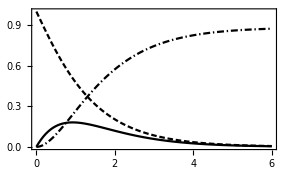

```mathematica
Plot[Evaluate[{F[γ],G[γ],H[γ]}],{γ,0,6},PlotPoints-> 100,PlotRange->{{0,6},{0,1}},PlotStyle-> {Black,Directive[AbsoluteDashing[{4,2}],Black],Directive[AbsoluteDashing[{5,2,1,2}],Black]},FrameLabel-> {Style["γ",FontFamily-> "Times New Roman"],None,None,None}]
```

Fig. Chapter.FigureCaption  Plot of F ——, G – – – – and H – • – • – which are the dimensionless velocities in the r, θ, and z directions respectively, versus the dimensionless distance, γ.

In recent versions of Mathematica the shooting method has been built into NDSolve. Here is an example of solving the above using the built in shooting method.

```mathematica
Clear[F,G,H];
result=NDSolve[{eqn1,eqn2,eqn3,G[0]==1,F[0]==0,H[0]==0,F[10]==0.,G[10]==0.},{F,G,H} ,{γ,0,10},Method->"BoundaryValues"->{"Shooting", "StartingInitialConditions"->{G[0]==1,F[0]==0,H[0]==0,F'[0]==0.5,G'[0]==-0.64}}]
```

{{F→InterpolatingFunction[{{0.,10.}},<>],G→InterpolatingFunction[{{0.,10.}},<>],H→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
{F,G,H}={F,G,H} /. res[[1]];

Plot[Evaluate[{F[γ],G[γ],H[γ]}],{γ,0,6},PlotPoints-> 100,PlotRange->{{0,6},{0,1}},PlotStyle-> {Black,Directive[AbsoluteDashing[{4,2}],Black],Directive[AbsoluteDashing[{5,2,1,2}],Black]},FrameLabel-> {Style["γ",FontFamily-> "Times New Roman"],None,None,None}]
```

-Graphics-

The vectors can be joined to form field lines showing the flow of fluid to the electrode surface. Beginning with a set of data:

```mathematica
data=Flatten[Table[{{r,-γ},Evaluate[{r*F[γ],H[γ]}]},{r,-5,5,.5},{γ,0,3,.2}],1];
```

The velocity vectors could be plotted using ListVectorPlot.

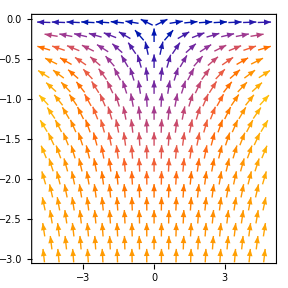

```mathematica
ListVectorPlot[data,AspectRatio-> 1,ImageSize-> {288,288}]
```

Alternatively the vectors could also be plotted directly using VectorPlot without firstly forming a list.

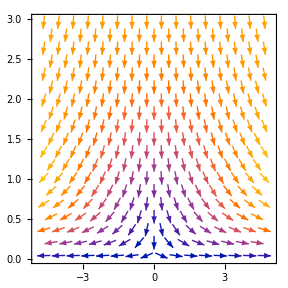

```mathematica
VectorPlot[Evaluate[{r*F[γ],-H[γ]}],{r,-5,5},{γ,0,3},AspectRatio-> 1,ImageSize-> {288,288}]
```

Interpolation functions are formed from the data list:

```mathematica
intr=Interpolation[Map[Part[Flatten[#],{1,2,3}]&,data]];
intγ=Interpolation[Map[Part[Flatten[#],{1,2,4}]&,data]];
```

The part assignment in the FieldLine function has been modified to accommodate this data.

```mathematica
(*modified FieldLine function*)
FieldLineMod[{x_,ex_InterpolatingFunction,x0_},{y_,ey_InterpolatingFunction,y0_},{t_,t1_}]:=Module[{exf,eyf,x1,y1,sol,t2,oldM},
exf[x1_,y1_]:=ex[x1,y1];
eyf[x1_,y1_]:=ey[x1,y1];
sol=NDSolve[{x'[t]==exf[x[t],y[t]],y'[t]==eyf[x[t],y[t]],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,t1}];
sol={x[t],y[t]}/.First[sol];
If[VectorQ[sol/.t->0,NumberQ],
t2=Part[sol,1,0,1,1,2](*<-- modified this bit*);
sol=ParametricPlot[Evaluate[sol],{t,0,t2}];
First[Cases[sol,Line[_],Infinity]],Line[{{x0,y0}}]
]
]
```

The FieldLineMod function is applied to a list of initial r values with the initial γ value being -3.

```mathematica
lines=Quiet@Join[
Table[FieldLineMod[{r,intr,i},{γ,intγ,-3.},{t,30.}],{i,-5,-.5,.5}],
{FieldLineMod[{r,intr,-.15},{γ,intγ,-3.},{t,60.}],FieldLineMod[{r,intr,.15},{γ,intγ,-3.},{t,60.}]},
Table[FieldLineMod[{r,intr,i},{γ,intγ,-3.},{t,30.}],{i,.5,5,.5}]
];
```

```mathematica
(* The function AddArrow from the old ExtendGraphics package is used to place arrows along the field lines. *)
ClearAll[AddArrow];
AddArrow[Line[opts_],d_,num_:5]:=Module[{arrow={},n=0,pts=Chop[opts]},
Fold[If[First[#1]≥d&&n<num,n++;
AppendTo[arrow,Arrow[{Last[#1],#2}]];
{0,#2},{First[#1]+Sqrt[Total[(Last[#1]-#2)^2]],#2}]&,{0,First[pts]},Rest[pts]];
arrow];
```

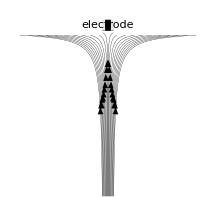

```mathematica
arrows=AddArrow[#,2.5,1]&/@lines;

Graphics[{Thickness[0.001],arrows,lines,{GrayLevel[0.9],Rectangle[{-5,.2},{5,0}]},{GrayLevel[0],Rectangle[{-2.5,.2},{2.5,0}]},Line[{{-5,0},{5,0}}],Text["electrode",{0,.1},BaseStyle-> {FontFamily-> "Arial",FontColor-> White,FontWeight-> Bold},FormatType-> TraditionalForm]},PlotRange-> {{-5,5},{.2,-3}},AspectRatio-> 1,ImageSize-> {216,216}]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  Fluid flow to a rotating disk electrode.

Make an animation in a separate window:

```mathematica
popUpAnimation[flow=Table[
arrows=AddArrow[#,j,1]&/@lines;Graphics[{Thickness[0.001],arrows,lines,{GrayLevel[0.9],Rectangle[{-5,.2},{5,0}]},{GrayLevel[0],Rectangle[{-2.5,.2},{2.5,0}]},Line[{{-5,0},{5,0}}],Text[Style["electrode",White],{0,.1},FormatType-> TraditionalForm]},PlotRange-> {{-5,5},{.2,-3}},AspectRatio-> 1,ImageSize-> {216,216}],{j,0,6,.3}],{320,260}];
```

```mathematica
(*Export the animation*)
Export["flow.gif",flow,"GIF","DisposalOperation"-> Background,"AnimationRepetitions"-> 10,"AnimationDisplayTime"-> .1]
```

flow.gif

## Chapter.Section Analytical solution

Having determined the velocity of the liquid to the rotating disk electrode, an expression for the current from a voltammetry experiment can be derived. We saw in the previous section that for reasons of symmetry all derivatives with respect to θ are zero and that the velocity of liquid in the z direction is independent of r and θ. At z=0 the boundary conditions are the same across the surface of the disk therefore ∂c(z,r, t)/∂r=0. The problem therefore can be written as a one dimensional problem given by

(∂c(z, t))/(∂t)=D(∂^2 c(z, t))/(∂z^2)-ν_z(∂c(z, t))/(∂z)

The rotating disk electrode is usually used under steady state conditions, i.e. ∂c(z, t)/∂t=0, therefore the equation that must be solved is

(d^2 c(z))/(d z^2)=ν_z/D(d c(z))/(d z)

with the boundary condition:

c(∞)=c^*

and v_z given by

v_z=-(ων)^(1/2)H(γ)

```mathematica
H=Normal[final⟦3⟧]
```

0.510214 γ^2-γ^3/3+0.102652 γ^4-0.0126448 γ^5

Substituting γ= (z(ω/ν))^(1/2) into eqn (Chapter.EquationNumbered) gives:

```mathematica
vz=Expand[-(ω*ν)^(1/2)*H/.γ-> z*(ω/ν)^(1/2)]
```

-(0.510214 z^2 ω √(ν ω))/ν-(0.102652 z^4 ω^2 √(ν ω))/ν^2+(z^3 ω √(ω/ν) √(ν ω))/(3 ν)+(0.0126448 z^5 ω^2 √(ω/ν) √(ν ω))/ν^2

Equation (Chapter.EquationNumbered) is generally solved by first substituting

b(z)=(dc(z))/(d z)

to give

(d b(z))/(d  z)=-(0.51  z^2 ω^(3/2))/(D ν^(1/2))b(z)

where v_1 is the first term of the series expression for v_z.

```mathematica
ode=b'[z]== vz⟦1⟧/𝒟*b[z]
```

b'[z]==-(0.510214 z^2 ω √(ν ω) b[z])/(𝒟 ν)

This equation can be solved using DSolve and with the boundary condition: b(0)=bO.

```mathematica
b[z]=b[z]/.First[DSolve[{ode,b[0]== bO},b[z],z]]
```

1. bO ⅇ^(-(0.170071 z^3 ω √(ν ω))/(𝒟 ν))

Substituting b(z)=(dc(z)/dz) and bO=(dc(z)/dz)_(z=0) and rearranging to integrate gives:

∫_0^(c^*) ⅆc=((∂c(z))/(∂z))_(z=0)∫_0^∞ exp(-(0.17  z^3 ω^(3/2))/(D ν^(1/2)))ⅆz

Integrating the right hand side of eqn (Chapter.EquationNumbered) gives

```mathematica
res=Integrate[b[z]/.bO-> c'[0],{z,0,∞},Assumptions-> {ω>0,ν>0,𝒟>0,Re[ω^2/(𝒟 √(ν ω))]>0}]
```

(1.61175 𝒟^(1/3) ν^(1/6) c'[0])/(√ω)

Solving for (dc(z)/dz)_(z=0) gives

```mathematica
(*  c^✶=bulk conc. Note that ✶ is "Esc*6Esc" and not "*"  *)

c'[0]=c'[0]/.First[Solve[(c^✶-c[0])== res,c'[0]]]
```

-(0.620443 √ω (-1. c^✶+1. c[0]))/(𝒟^(1/3) ν^(1/6))

and since the current is defined as

i(t)=-n F A (D((∂c(z))/(∂z)))_(z=0)

the steady state current for rotating disk voltammetry is

```mathematica
ClearAll[F];
n*F*A*𝒟*c'[0]//Simplify
```

(0.620443 A F n 𝒟^(2/3) √ω (1. c^✶-1. c[0]))/ν^(1/6)

The current can be written as

i(t)=-(n F A D(c^*-c(0)))/δ

where δ is known as the diffusion layer thickness and is given by

δ=1.612 D^(1/3)ν^(1/6)ω^(-1/2)

```mathematica
δ=res/c'[0]
```

(1.61175 𝒟^(1/3) ν^(1/6))/(√ω)

## Chapter.Section Finite differences solution

The diffusion-convection equation, eqn (Chapter.EquationNumbered), can be made dimensionless by substituting t=σ t, where as in earlier chapters σ=n F υ/R T, c(z, t)=c(z, t)/c^* and z=z/δ to give

(∂c(z,t))/(∂t)=D/σδ^2(∂^2 c(z,t))/(∂z^2)-(v_z δ)/D D/σδ^2(∂c(z,t))/(∂z)

and

v_z=-0.510 ω^(3/2)ν^(-1/2)δ^2 z^2

For now only the first term of series expansion of v_z will be used but higher order terms could be included if desired. The term v_z δ/D can be simplified to:

```mathematica
ClearAll[vZ,𝕫];

vZ=(-0.510*ω^(3/2)*ν^(-1/2)*δ^2*𝕫^2)*δ/𝒟
```

-2.13532 𝕫^2

The dimensionless parameter σδ^2/D can be expanded to show that its magnitude indicates the ratio of the potential sweep rate and disk rotation rate.

Δ=σδ^2/D
=(n F)/(R T)(2.6  ν^(1/3))/D^(1/3)υ/ω

The experiment approaches steady state as Δ→0. Equation (Chapter.EquationNumbered) can be re-written as

(∂c(z,t))/(∂t)=1/Δ(∂^2 c(z,t))/(∂z^2)+(2.135 z^2)/Δ(∂c(z,t))/(∂z)

Re-writing eqn (Chapter.EquationNumbered) in discrete forms gives

(c_j^(k+1)-c_j^k)/Δt=1/Δ(c_(j+1)^k-2 c_j^k+c_(j-1)^k)/(Δz)^2+(2.135 z^2)/Δ(c_(j+1)^k-c_(j-1)^k)/(2Δz)

or

(c_j^(k+1)-c_j^k)=D((c_(j+1)^k-2 c_j^k+c_(j-1)^k)+(2.135(z_j)^2 Δz)/2(c_(j+1)^k-c_(j-1)^k))

with

D=Δt/((Δz)^2 Δ)

The flux, J, of O is

J(j,k)=-c_O^*D_O/δΔz(3 c_O_j^k-4 c_(O_(j+1))^k+c_(O_(j+2))^k)/2

The current is therefore

i(k)=-n F A J(1,k)=n F A c_O^*D_O/(2δΔz)(3 c_O_1^k-4 c_O_2^k+c_O_3^k)

Substituting (m-1)Δ z=z_max into eqn (Chapter.EquationNumbered) and dividing both sides by Δ^(1/2) gives the dimensionless current.

π^(1/2)χ(σt)=(i(t))/(n F A c_O^* (σ D_O)^(1/2))=(m-1)/(2 Δ^(1/2)z_max)(3 c_O_1^k-4 c_O_2^k+c_O_3^k)

An expression for the dimensionless rate constant can be derived from the Butler Volmer equation:

(i(k))/(n F A c_O^*)=k_s(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

with

ξ=exp((nF/RT)(E-E°'))

By multiply both sides of eqn (24) by δ/(D_O Δ^(1/2)) the dimensionless current is obtained.

π^(1/2)χ(k)=(i(k))/(n F A c_O^* (σ D_O)^(1/2))=k_s(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

where

k_s=k_s δ/(D_O Δ^(1/2))

Equating eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) gives

3 c_O_1^k-4 c_O_2^k+c_O_3^k=k_s^*(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

with

k_s^*=(2 δz_max k_s)/(D_O(m-1))

### Chapter.Section.Subsection Steady state voltammetry

At steady state

(∂c(z, t))/(∂t)=0

therefore eqn (Chapter.EquationNumbered) becomes

(c_(j+1)^k-2 c_j^k+c_(j-1)^k)+(2.135(z_j)^2 Δz)/2(c_(j+1)^k-c_(j-1)^k)=0

Substituting z_j=(j-1)Δz and Δz=z_max/(m-1) into eqn (Chapter.EquationNumbered) gives

(c_(j-1)^k-2 c_j^k+c_(j+1)^k)+(2.135(j-1)^2(z_max)^3)/(2(m-1)^3)(c_(j+1)^k-c_(j-1)^k)=0

The system of equations to be solved is

x_2 c_1^(k+1)+y_2 c_2^(k+1)+z_2 c_3^(k+1)=0
x_3 c_2^(k+1)+y_3 c_3^(k+1)+z_3 c_4^(k+1)=0
⋮
x_j c_(j-1)^(k+1)+y_j c_j^(k+1)+z_j c_(j+1)^(k+1)=0
⋮
x_(m-1)c_(m-2)^(k+1)+y_(m-1)c_(m-1)^(k+1)=-z_(m-1)c_m^(k+1)

with

x_j=(1-(2.135(j-1)^2(z_max)^3)/(2(m-1)^3))

y_j=-2

and

z_j=(1+(2.135(j-1)^2(z_max)^3)/(2(m-1)^3))

The surface boundary value, c_O_1^k, is (§7.5)

c_O_1^k=(2 k_s^*ξ+ξ^α(4 c_O_2^k-c_O_3^k))/(3 ξ^α+2k_s^*(1+ξ))

Therefore the first line of eqn (Chapter.EquationNumbered) becomes

y_2 c_2^(k+1)+z_2 c_3^(k+1)=u_2

with

y_2=((4 x_2 ξ^α)/(3 ξ^α+2k_s^*(1+ξ))-2)

z_2=(1+(2.135(z_max)^3)/(2(m-1)^3)-(x_2 ξ^α)/(3 ξ^α+2k_s^*(1+ξ)))

and

u_2=-(2 x_2 k_s^*ξ)/(3 ξ^α+2k_s^*(1+ξ))

with x_2 given by eqn (Chapter.EquationNumbered). The voltammogram is readily simulated using the voltammetric simulation methods described in earlier chapters but with modified diagonals.

makeDiagonals[m_Integer,zMax_]:=Module[{x,y,z,β},
β=(2.13496*zMax^3*(j-1)^2)/(2.*(m-1)^3);
x=Table[1-β,{j,2,m-1}];
z=Table[1+β,{j,2,m-2}];
y=Table[-2.,{j,2,m-1}];
{x,y,z}]

implicitSolveRDESS[m_Integer,n_Integer,{lowerLimit_,upperLimit_},{ksStar_,α_,zMax_}]:=Module[{x,y,z,len,mat,x1,y1,z1,initial,range,τ,solveNext,zM},

range=(upperLimit+Abs[lowerLimit]);
τ=range/(n-1.);

{x,y,z}=makeDiagonals[m,zMax];
len=Length[y];
mat=SparseArray[{Band[{2,1}]→x,Band[{1,1}]→y,Band[{1,2}]→z},len];
initial=ConstantArray[1.,{m}];
x1=1-(2.13496*zMax^3)/(2.*(m-1)^3);
y1=y⟦1⟧;
z1=z⟦1⟧;
zM=1.+(2.13496*zMax^3*(j-1)^2)/(2.*(m-1)^3)/.j→ (m-1);

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2},
ξ=Exp[upperLimit-(τ*(k-1))];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=ConstantArray[0.,{m-2}];
b⟦1⟧-=(tmp*x1*ksStar*ξ^(1.-α));
b⟦-1⟧-=zM;
mat⟦1,1⟧=y1+4.*x1*tmp;
mat⟦1,2⟧=z1-x1*tmp;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]];

Rest@FoldList[solveNext,initial,Range[2,n]]
]

The full implementation is given in the notebook implicitRDESS.nb.

Figure Chapter.FigureCaption shows a simulated steady state voltammogram.

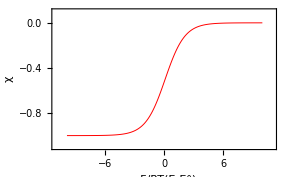

Fig. Chapter.FigureCaption  Simulated steady state reversible voltammogram. Simulation parameters: m=100.

### Chapter.Section.Subsection Non-steady state voltammetry

Rearranging eqn (Chapter.EquationNumbered) gives

((2.135(z_j)^2 Δz)/2-1)D  c_(j-1)^(k+1)+(1+2D)c_j^(k+1)-(1+(2.135(z_j)^2 Δz)/2)D  c_(j+1)^(k+1)=c_j^k

Substituting z_j=(j-1)Δz and Δz=z_max/(m-1) into eqn (Chapter.EquationNumbered) gives

((2.135(j-1)^2(z_max)^3)/(2(m-1)^3)-1)D  c_(j-1)^(k+1)+(1+2D)c_j^(k+1)-(1+(2.135(j-1)^2(z_max)^3)/(2(m-1)^3))D  c_(j+1)^(k+1)=c_j^k

The system of equations to be solved is

x_2 c_1^(k+1)+y_2 c_2^(k+1)+z_2 c_3^(k+1)=c_2^k
x_3 c_2^(k+1)+y_3 c_3^(k+1)+z_3 c_4^(k+1)=c_3^k
⋮
x_j c_(j-1)^(k+1)+y_j c_j^(k+1)+z_j c_(j+1)^(k+1)=c_j^k
⋮
x_(m-1)c_(m-2)^(k+1)+y_(m-1)c_(m-1)^(k+1)=c_(m-1)^k-z_(m-1)c_m^(k+1)

with

x_j=((2.135(j-1)^2(z_max)^3)/(2(m-1)^3)-1)D

y_j=1+2D

and

z_j=-(1+(2.135(j-1)^2(z_max)^3)/(2(m-1)^3))D

The surface boundary value, c_O_1^k, is

c_O_1^k=(2 k_s^*ξ+ξ^α(4 c_O_2^k-c_O_3^k))/(3 ξ^α+2k_s^*(1+ξ))

Therefore the first line of eqn (Chapter.EquationNumbered) becomes

y_2 c_2^(k+1)+z_2 c_3^(k+1)=u_2

with

y_2=((4 x_2 ξ^α)/(3 ξ^α+2k_s^*(1+ξ))+1+2D)

z_2=(-(1+(2.135(z_max)^3)/(2(m-1)^3))D-(x_2 ξ^α)/(3 ξ^α+2k_s^*(1+ξ)))

and

u_2=c_2^k-(2 x_2 k_s^*ξ)/(3 ξ^α+2k_s^*(1+ξ))

with x_2 given by eqn (Chapter.EquationNumbered). The voltammogram is readily simulated using the voltammetric simulation methods described in earlier chapters but with modified diagonals.

makeDiagonals[m_Integer,d_][zMax_]:=Module[{x,y,z},
x=Table[-d+(2.13496*zMax^3*d*(j-1)^2)/(2.*(m-1)^3),{j,3,m-1}];
z=Table[-d-(2.13496*zMax^3*d*(j-1)^2)/(2.*(m-1)^3),{j,2,m-2}];
y=Table[1.+2.*d,{j,2,m-1}];
{x,y,z}]

implicitSolveRDE[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_},{ksStar_,α_,zMax_}]:=Module[{x,y,z,len,mat,x1,y1,z1,initial,range,τ,solveNext,zM},

range=2*(upperLimit+Abs[lowerLimit]);
τ=range/(n-1.);

{x,y,z}=makeRDEDiagonals[m,d][zMax];
len=Length[y];
mat=SparseArray[{Band[{2,1}]→x,Band[{1,1}]→y,Band[{1,2}]→z},len];
initial=ConstantArray[1.,{m}];
x1=-d+(2.13496*zMax^3*d)/(2.*(m-1)^3);
y1=y⟦1⟧;
z1=z⟦1⟧;
zM=-d-(2.13496*zMax^3*d*(j-1)^2)/(2.*(m-1)^3)/.j→ (m-1);

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2},
ξ=If[k>(n+1)/2,Exp[upperLimit-range+(τ*(k-1))],Exp[upperLimit-(τ*(k-1))]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=list[[2;;-2]];
b⟦1⟧-=(tmp*x1*ksStar*ξ^(1.-α));
b⟦-1⟧-=zM;
mat⟦1,1⟧=y1+4.*x1*tmp;
mat⟦1,2⟧=z1-x1*tmp;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]];

Rest@FoldList[solveNext,initial,Range[2,n]]
]

The full implementation is given in the notebook implicitRDE.nb.

Figure Chapter.FigureCaption shows a simulated non-steady state rotating disk voltammogram.

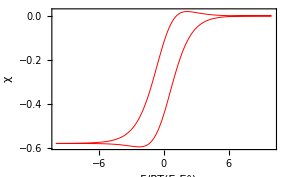

Fig. Chapter.FigureCaption  Simulated rotating disk voltammogram. Simulation parameters: Δ=3.0; k_s=20; D=10.

## Further reading

Albery, W. J. and Hitchman, M. L. (1971). Ring Disk Electrodes, Clarendon Press, Oxford.
Feldberg, S. W., Goldstein, C. I., and Rudolph, M. (1996). Journal of Electroanalytical Chemistry, 413, 25-36.
Filinovsky, V. Y. and Pleskov, Y. V. (1984). Rotating Disk and Ring-Disk Electrodes. In Comprehensive Treatise of Electrochemistry, Vol. 9. (eds. E. Yeager, J. O. M. Bockris, B. E. Conway, and S. Sarangapani), pp. 293-352. Plenum, New York.
Newman, J. S. (1991). Electrochemical Systems, (2nd edn). Prentice Hall, Englewood Cliffs.
Riddiford, A. C. (1966). The Rotating Disk System. In Advances in Electrochemistry and Electrochemical Engineering, Vol. 4. (ed. P. Delahay), pp. 47-116. Wiley, New York.